```mathematica
Reduce[7==-4/56-56 c,c]
```

c==-99/784

```mathematica
Expand[1+7x+3x^4-(-1/(56x)-99/784)(-56x+4x^2+5x^3-32x^4)]
```

(233 x^2)/392+(47 x^3)/784-(51 x^4)/49

```mathematica
Reduce[CoefficientList[(-56x+4x^2+5x^3-32x^4),x][[1;;3]]==CoefficientList[(c1/x+c0)((233 x^2)/392+(47 x^3)/784-(51 x^4)/49),x][[1;;3]],{c0,c1}]
```

c0==881216/54289&&c1==-21952/233

```mathematica
Expand[(-56x+4x^2+5x^3-32x^4)-((233 x^2)/392+(47 x^3)/784-(51 x^4)/49)(c1/x+c0)/.{c0->881216/54289,c1->-21952/233}]
```

-(5104967 x^3)/54289-(820064 x^4)/54289

```mathematica
Reduce[CoefficientList[((233 x^2)/392+(47 x^3)/784-(51 x^4)/49),x][[1;;4]]==CoefficientList[(c1/x+c0)(-(5104967 x^3)/54289-(820064 x^4)/54289),x][[1;;4]],{c0,c1}]
```

c0==22509576625/59567287019632&&c1==-12649337/2001147064

```mathematica
Expand[((233 x^2)/392+(47 x^3)/784-(51 x^4)/49)-(-(5104967 x^3)/54289-(820064 x^4)/54289)(c1/x+c0)/.{c0->22509576625/59567287019632,c1->-12649337/2001147064}]
```

-(550523087689 x^4)/531850776961

```mathematica
Reduce[CoefficientList[(-(5104967 x^3)/54289-(820064 x^4)/54289),x][[1;;5]]==CoefficientList[(c1/x+c0)(-(550523087689 x^4)/531850776961),x][[1;;5]],{c0,c1}]
```

c0==436151675557745504/29887347907548121&&c1==2715080665310265287/29887347907548121

```mathematica
Expand[(-(5104967 x^3)/54289-(820064 x^4)/54289)-(-(550523087689 x^4)/531850776961)(c1/x+c0)/.{c0->436151675557745504/29887347907548121,c1->2715080665310265287/29887347907548121}]
```

0

```mathematica
FullSimplify[FromContinuedFraction[{8, -1/(56x)-99/784,881216/54289-21952/(233x), 22509576625/59567287019632-12649337/(2001147064x),436151675557745504/29887347907548121+2715080665310265287/(29887347907548121x)}]]
```

(8+x^2 (4+(5-8 x) x))/(1+7 x+3 x^4)

```mathematica
ExpandNumerator[%]
```

(8+4 x^2+5 x^3-8 x^4)/(1+7 x+3 x^4)

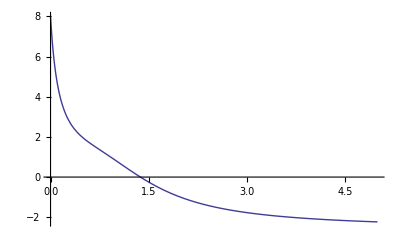

```mathematica
Plot[(8+4 x^2+5 x^3-8 x^4)/(1+7 x+3 x^4),{x,0,5}]
```

```mathematica
Reduce[-1/(56x)-99/784==0,x]
```

x==-14/99

```mathematica
1+7 x+3 x^4/.{x->-14/99}
```

361849/32019867

```mathematica
NSolve[1+7 x+3 x^4==0,x]
```

{{x→-1.27483},{x→-0.143037},{x→0.708935-1.15127 ⅈ},{x→0.708935+1.15127 ⅈ}}

```mathematica
N[-14/99]
```

-0.141414

```mathematica
Reduce[881216/54289-21952/(233x)==0,x]
```

x==1631/281

```mathematica
N[1631/281]
```

5.80427

```mathematica
NSolve[8+4 x^2+5 x^3-8 x^4==0,x]
```

{{x→-0.973298},{x→0.112051-0.857383 ⅈ},{x→0.112051+0.857383 ⅈ},{x→1.3742}}

```mathematica
FullSimplify[Convergents[{8, -1/(56x)-99/784,881216/54289-21952/(233x), 22509576625/59567287019632-12649337/(2001147064x),436151675557745504/29887347907548121+2715080665310265287/(29887347907548121x)}]]
```

{8,(8 (14+x))/(14+99 x),(8 (1864+x (-188+1085 x)))/(1864+(12860-1163 x) x),(833464+x (-133888+x (1889692+70963 x)))/(104183+x (712545+4 x (16742+310241 x))),(8+x^2 (4+(5-8 x) x))/(1+7 x+3 x^4)}

```mathematica
NSolve[1864+(12860-1163 x) x==0,x]
```

{{x→-0.143094},{x→11.2007}}

```mathematica
NSolve[104183+x (712545+4 x (16742+310241 x))==0,x]
```

{{x→-0.143039},{x→0.044537-0.764816 ⅈ},{x→0.044537+0.764816 ⅈ}}

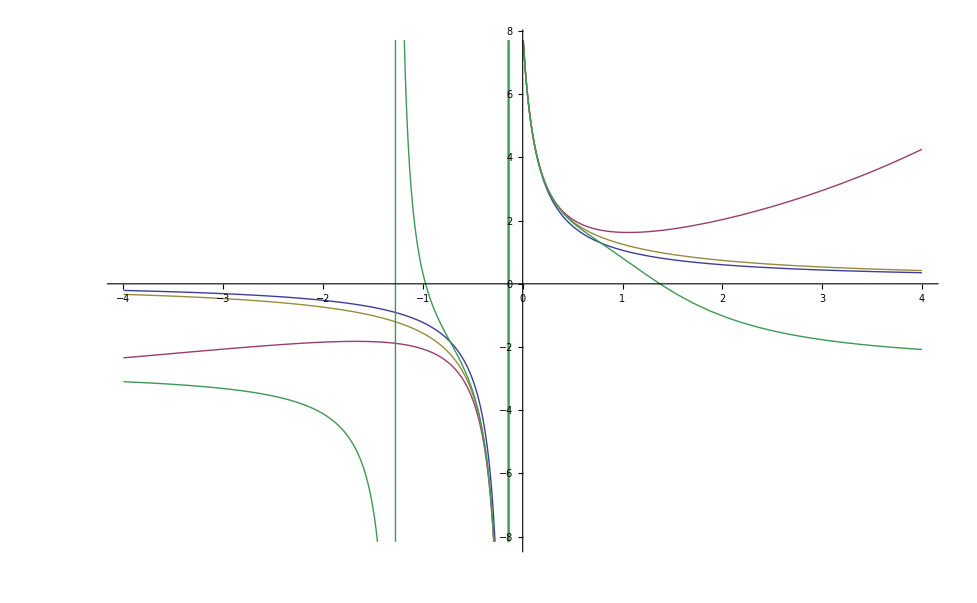

```mathematica
Plot[{(8 (14+x))/(14+99 x),(8 (1864+x (-188+1085 x)))/(1864+(12860-1163 x) x),(833464+x (-133888+x (1889692+70963 x)))/(104183+x (712545+4 x (16742+310241 x))),(8+x^2 (4+(5-8 x) x))/(1+7 x+3 x^4)},{x,-4,4}]
```

```mathematica
ExpandNumerator[(8 (1864+x (-188+1085 x)))/(1864+(12860-1163 x) x)]
```

(14912-1504 x+8680 x^2)/(1864+(12860-1163 x) x)

```mathematica
ExpandNumerator[FullSimplify[(8-188/233x+1085/233x^2)/(1+3215/466 x-1163/1864x^2)]]
```

(14912-1504 x+8680 x^2)/(1864+(12860-1163 x) x)